```mathematica
D[(1-(1-z)b)^n, {z, m}]
```

b^m (1-b (1-z))^(-m+n) FactorialPower[n,m]

```mathematica
Clear[ntot];
KT = 414/100;
k0=1;
eta[ka_, kb_]:=ka / (ka + kb);
koff[eb_, xb_, f_]:= (10^3)Exp[-eb + f xb / KT];
```

```mathematica
Clear[Pm, mAve];
Pm[m_, t_, eb_,ea_, nc_]:=Module[{xa=1.5, xb=2.0, f=0},
koffAPC = koff[ea, xa, f];
koffb = koff[eb, xb, f];
a = koffb + koffAPC;
If[t==0,If[m==nc, 1, 0],
Exp[-a t m](1- Exp[-a t])^(nc-m)FactorialPower[nc, m]/Factorial[m]
]]

mAve[t_, eb_,ea_, nc_]:=Sum[m Pm[m, t, eb, ea, nc], {m, 0, nc}]
```

```mathematica
mAve[1, 10, 10, 20]
```

18.264

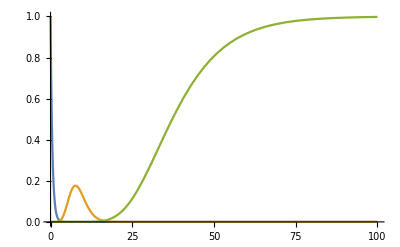

```mathematica
Plot[{
Pm[20, tx, 10, 20],
Pm[10, tx, 10, 20],
Pm[0, tx, 10, 20]
}, {tx,0, 100}, PlotRange->All]
```

```mathematica
Clear[fisherInfo, fisherInfo2]
fisherInfo[t_, eb_, nc_]:=Module[{xa=1.5, xb=2.0, ea=10, f=0},
koffAPC = koff[ea, xa, f];
koffb = koff[eb, xb, f];
a = koffb + koffAPC;
etaT= Exp[-a t];
Sum[Binomial[nc, mx] etaT^mx (1-etaT)^(nc-mx-2) koffb^2 t^2 (nc * etaT - mx)^2, {mx,0, nc}]
]

fisherInfo2[t_, eb_, ea_, nc_]:=Module[{xa=1.5, xb=2.0, f=0},
koffAPC = koff[ea, xa, f];
koffb = koff[eb, xb, f];
a = koffb + koffAPC;
nc koffb^2 t^2 Exp[-a t]/ (1-Exp[-a t])
]
fisherInfo[50, 10, 20]
fisherInfo2[50, 10,10, 20]
```

1.11185

1.11185

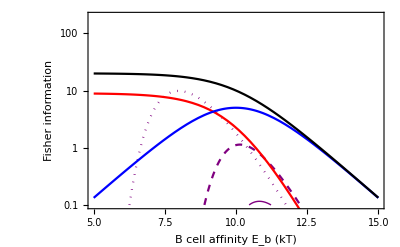

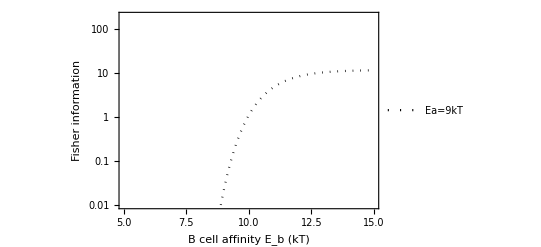

```mathematica
Show[
LogPlot[
{
fisherInfo2[5, ebx, 10,20],
fisherInfo2[50, ebx, 10, 20],
fisherInfo2[100, ebx, 10, 20]
}, {ebx, 5, 15},
PlotRange->{0.1, 200},
PlotStyle->{{Purple, Dotted}, {Purple, Dashed}, {Purple, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"B cell affinity E_b (kT)", "Fisher information"}
],

LogPlot[
Log[20]^2/(1+Exp[eb-10])^2, {eb, 5, 15}, PlotStyle->Red],
LogPlot[
20 * Exp[eb-10]/(1+Exp[eb-10])^2, {eb,5,15}, PlotStyle->Blue
],
LogPlot[
20 /(1+Exp[eb-10]), {eb,5,15}, PlotStyle->Black
]

]
```

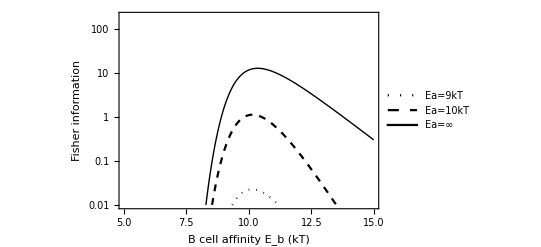

```mathematica
LogPlot[
{
fisherInfo2[50, ebx,  9, 20],
fisherInfo2[50, ebx, 10, 20],
fisherInfo2[50, ebx, 200, 20]
}, {ebx, 5, 15},
PlotRange->{0.01, 200},
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.2, 0.8}],
FrameStyle->Directive[14],
FrameLabel->{"B cell affinity E_b (kT)", "Fisher information"}
]
```

```mathematica
LogPlot[
{
fisherInfo2[50, ebx,  9],
fisherInfo2[50, ebx, 10],
fisherInfo2[50, ebx, 15]
}, {ebx, 5, 15},
PlotRange->{0.01, 200},
PlotStyle->{{Purple, Dotted}, {Purple, Dashed}, {Purple, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"B cell affinity E_b (kT)", "Fisher information"}
]
```

```mathematica
D[t^2 Exp[-b t]/(1-Exp[- b t]), t]
```

(2 ⅇ^(-b t) t)/(1-ⅇ^(-b t))-(b ⅇ^(-2 b t) t^2)/((1-ⅇ^(-b t))^2)-(b ⅇ^(-b t) t^2)/(1-ⅇ^(-b t))

```mathematica
Solve[(2 ⅇ^(-b t) t)/(1-ⅇ^(-b t))-(b ⅇ^(-2 b t) t^2)/((1-ⅇ^(-b t))^2)-(b ⅇ^(-b t) t^2)/(1-ⅇ^(-b t))==0, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(2+ProductLog[-2/ⅇ^2])/b}}

```mathematica
2.0+ProductLog[-2/ⅇ^2]
```

1.59362

```mathematica
t^2 Exp[-b t]/(1-Exp[- b t]) /.t->(2+ProductLog[-2/ⅇ^2])/b
```

(ⅇ^(-2-ProductLog[-2/ⅇ^2]) (2+ProductLog[-2/ⅇ^2])^2)/(b^2 (1-ⅇ^(-2-ProductLog[-2/ⅇ^2])))

```mathematica
Simplify[%]
```

((2+ProductLog[-2/ⅇ^2])^2)/(b^2 (-1+ⅇ^(2+ProductLog[-2/ⅇ^2])))

```mathematica
FullSimplify[%]
```

-(ProductLog[-2/ⅇ^2] (2+ProductLog[-2/ⅇ^2]))/b^2

```mathematica
ProductLog[-2.0/ⅇ^2] (2+ProductLog[-2/ⅇ^2])
```

-0.64761

```mathematica
Clear[a, b]
DSolve[y'[x]== a Exp[-a x]-b y[x], y[x], x]
```

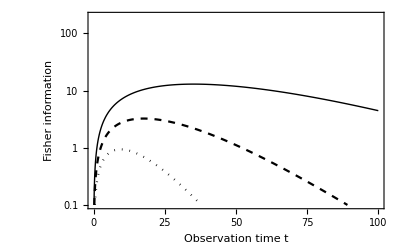

```mathematica
LogPlot[
{
fisherInfo2[tx, 10,  9, 20],
fisherInfo2[tx, 10, 10, 20],
fisherInfo2[tx, 10,200, 20]
}, {tx, 0, 100},
PlotRange->{0.1, 200},
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]
```

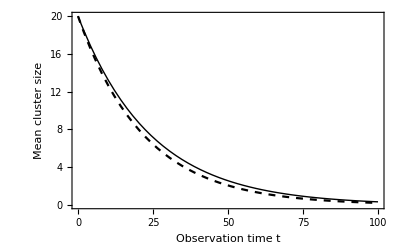

```mathematica
Plot[
{
mAve[tx, 10,  200, 20],
mAve[tx, 10.1, 200, 20]
(*mAve[tx, 10,200, 20]*)
}, {tx, 0, 100},
PlotRange->{0, 20},
PlotStyle->{ {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Mean cluster size"}
]
```

## Coupled ODE

```mathematica
Clear[PmF, nc]
PmF[m_, t_, eb_, f_, ea_, nc_]:=Module[{xa=3/2, xb=2},
Clear[fa, fb, koffAPC, koffb];
fa= f*xa / KT;
fb = f * xb / KT;
koffAPC = koff[ea, xa, 0];
koffb = koff[eb, xb, 0];
Clear[a, ret];
a[n_]:=n*koffAPC*Exp[fa / n] + n * koffb * Exp[fb/n];
If[m==nc, 
ret=Exp[-a[m]t]
,{
If[m>0,
ret = Product[a[i], {i, m+1, nc}]*Sum[ (Exp[(a[m]-a[i])t] - 1)/(Product[(a[j] - a[i]), {j, m, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, m+1, nc}]Exp[-a[m]t],
ret= Product[a[i], {i, 1, nc}]*Sum[ (-(Exp[-a[i]t]-1)/a[i] + (Exp[-a[1]t]-1)/a[1])/(Product[(a[j] - a[i]), {j, 1, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, 2, nc}]
];}];
ret

]

mAveF[t_, eb_, f_, ea_, nc_]:=Sum[m PmF[m, t,eb,f,ea, nc],{m, 0, nc}]

PmFInfEa[m_, t_, eb_, f_, nc_]:=Module[{ xb=2},
Clear[fa, fb, koffAPC, koffb];
fb = f * xb / KT;
koffb = koff[eb, xb, 0];
Clear[a, ret];
a[n_]:= n * koffb * Exp[fb/n];
If[m==nc, 
ret=Exp[-a[m]t]
,{
If[m>0,
ret = Product[a[i], {i, m+1, nc}]*Sum[ (Exp[(a[m]-a[i])t] - 1)/(Product[(a[j] - a[i]), {j, m, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, m+1, nc}]Exp[-a[m]t],
ret= Product[a[i], {i, 1, nc}]*Sum[ (-(Exp[-a[i]t]-1)/a[i] + (Exp[-a[1]t]-1)/a[1])/(Product[(a[j] - a[i]), {j, 1, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, 2, nc}]
];}];
ret

]

mAveFInfEa[t_, eb_, f_,  nc_]:=Sum[m PmFInfEa[m, t,eb,f, nc],{m, 0, nc}]
```

```mathematica
N[PmF[0, 20, 10, 10, 200, 20], 9]
N[PmFInfEa[0,20, 10, 10, 20], 9]
```

0.247203924

0.247203924

```mathematica
Pm[0, 20, 10, 20]
```

0.0286995

```mathematica
Sum[PmF[mi, 20, 10, 0, 10, 30], {mi, 0, 30}]
```

1.

```mathematica
PmF[20, 5, 10, 4, 10, 20]
```

0.0000511003

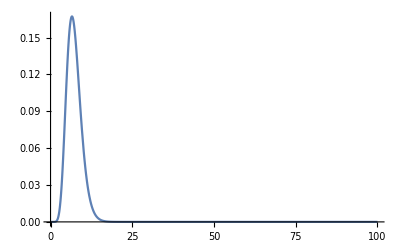

```mathematica
Plot[PmF[10, tx, 10, 5, 10, 20],{tx,0, 100}, PlotRange->All]
```

### Fisher information

```mathematica
Clear[q, fisherInfoF]
```

```mathematica
fisherInfoF[t_, eb_, ea_, f_, nc_]:=Module[{xaF=3/2, xbF=2},
Clear[q, dPdE,faF,fbF,koffAPCF, koffbF];
q[m_]:=koff[eb, xbF, f/m] / (koff[ea, xaF, f/m] + koff[eb, xbF, f/m]);
faF= f*xaF / KT;
fbF = f * xbF / KT;
koffAPCF = koff[ea, xaF, 0];
koffbF = koff[eb, xbF, 0];
Clear[aF];
aF[n_]:=n*koffAPCF*Exp[faF / n] + n * koffbF * Exp[fbF/n];

dPdE[m_]:= -Sum[q[i], {i, m+1, nc}]PmF[m, t, eb, f, ea, nc] + (Product[aF[i], {i, m+1, nc}])Sum[
(
aF[i]q[i]t Exp[-aF[i]t] - aF[m]q[m]t Exp[-aF[m]t] + (Exp[-aF[i]t]-Exp[-aF[m]t]) (Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, m, i-1}] + Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, i+1, nc}])
)/(
Product[aF[j]-aF[i], {j, m, i-1}] * Product[aF[j]-aF[i], {j, i+1, nc}]
)
, {i, m+1, nc}];


dPdE0 =-Sum[q[i], {i,1,nc}]PmF[0, t,eb,f,ea, nc] +(Product[aF[i], {i, 1, nc}])Sum[
(
-q[i](1+aF[i]t)Exp[-aF[i]t]/aF[i]+q[i]/aF[i] +q[1](1+aF[1]t)Exp[-aF[1]t]/aF[1]-q[1]/aF[1]+(-(Exp[-aF[i]t]-1)/aF[i] + (Exp[-aF[1]t]-1)/aF[1])(
Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, 1, i-1}]+Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, i+1, nc}]
)
)/(Product[(aF[j] - aF[i]), {j, 1, i-1}]*Product[(aF[j]-aF[i]),{j, i+1, nc}])
, {i,2, nc}];

(*Print["dPdE0=", dPdE0 ];
Print["P[0]=", PmF[0, t,eb,f,ea, nc] ];
Print["dPdE1=", dPdE[1]];
Print["P[1]=", PmF[1,t,eb,f,ea, nc]];
Print["part1=", dPdE0^2 / PmF[0, t,eb,f,ea, nc]];
Print["part2=", Sum[(dPdE[m])^2 / PmF[m, t, eb, f, ea, nc] , {m, 1, nc-1}]];
Print["part3=",PmF[nc, t, eb,f,ea, nc]*(aF[nc]*t*q[nc])^2 ];*)
dPdE0^2 / PmF[0, t,eb,f,ea, nc]+Sum[(dPdE[m])^2 / PmF[m, t, eb     , f, ea, nc] , {m, 1, nc-1}] + PmF[nc, t, eb,f,ea, nc]*(aF[nc]*t*q[nc])^2
]
Print["Actual:   ", N[fisherInfoF[50, 10, 10, 0, 20], 9]]
Print["Expected: ", fisherInfo2[50, 10, 10, 20]]
```

Actual:   1.11185158

Expected: 1.11185

```mathematica
fisherInfoFInfEa[t_, eb_, f_, nc_]:=Module[{xbF=2},
Clear[q, dPdE,faF,fbF,koffAPCF, koffbF];
q[m_]:=1;
fbF = f * xbF / KT;
koffbF = koff[eb, xbF, 0];
Clear[aF];
aF[n_]:= n * koffbF * Exp[fbF/n];

dPdE[m_]:= -Sum[q[i], {i, m+1, nc}]PmFInfEa[m, t, eb, f, nc] + (Product[aF[i], {i, m+1, nc}])Sum[
(
aF[i]q[i]t Exp[-aF[i]t] - aF[m]q[m]t Exp[-aF[m]t] + (Exp[-aF[i]t]-Exp[-aF[m]t]) (Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, m, i-1}] + Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, i+1, nc}])
)/(
Product[aF[j]-aF[i], {j, m, i-1}] * Product[aF[j]-aF[i], {j, i+1, nc}]
)
, {i, m+1, nc}];


dPdE0 =-Sum[q[i], {i,1,nc}]PmFInfEa[0, t,eb,f, nc] +(Product[aF[i], {i, 1, nc}])Sum[
(
-q[i](1+aF[i]t)Exp[-aF[i]t]/aF[i]+q[i]/aF[i] +q[1](1+aF[1]t)Exp[-aF[1]t]/aF[1]-q[1]/aF[1]+(-(Exp[-aF[i]t]-1)/aF[i] + (Exp[-aF[1]t]-1)/aF[1])(
Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, 1, i-1}]+Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, i+1, nc}]
)
)/(Product[(aF[j] - aF[i]), {j, 1, i-1}]*Product[(aF[j]-aF[i]),{j, i+1, nc}])
, {i,2, nc}];

(*Print["dPdE0=", dPdE0 ];
Print["P[0]=", PmF[0, t,eb,f,ea, nc] ];
Print["dPdE1=", dPdE[1]];
Print["P[1]=", PmF[1,t,eb,f,ea, nc]];
Print["part1=", dPdE0^2 / PmF[0, t,eb,f,ea, nc]];
Print["part2=", Sum[(dPdE[m])^2 / PmF[m, t, eb, f, ea, nc] , {m, 1, nc-1}]];
Print["part3=",PmF[nc, t, eb,f,ea, nc]*(aF[nc]*t*q[nc])^2 ];*)
dPdE0^2 / PmFInfEa[0, t,eb,f, nc]+Sum[(dPdE[m])^2 / PmFInfEa[m, t, eb     , f,  nc] , {m, 1, nc-1}] + PmFInfEa[nc, t, eb,f, nc]*(aF[nc]*t*q[nc])^2
]
Print["Actual:   ", 1.0 fisherInfoFInfEa[50, 10, 0, 20]]
Print["Expected: ", 1.0 fisherInfo2[50, 10, 200, 20]]

Print["Actual:   ",1.0 fisherInfoFInfEa[50, 10, 5, 20]]
Print["Expected: ", 1.0 fisherInfoF[50, 10, 200, 5, 20]]
```

Actual:   11.8739

Expected: 11.8739

Actual:   6.39706

Expected: 6.39706

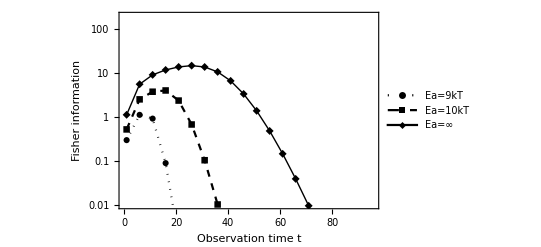

```mathematica
Show[ListLogPlot[
{
Table[{tx, fisherInfoF[tx, 10,  9, 7, 20]}, {tx, 1, 100, 5}],
Table[{tx, fisherInfoF[tx, 10,  10, 7, 20]}, {tx, 1, 100, 5}],
Table[{tx, fisherInfoFInfEa[tx, 10,  7, 20]}, {tx, 1, 100, 5}]
}, 
PlotRange->{0.01, 200},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]

]
```

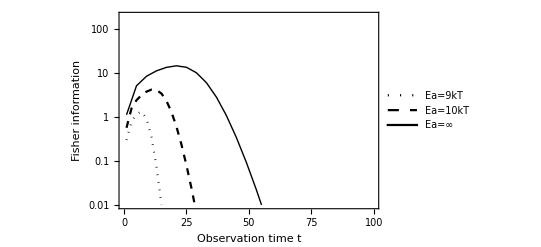

```mathematica
$MaxExtraPrecision = 500;
Show[ListLogPlot[
{
Table[{tx, N[fisherInfoF[tx, 10,  9, 10, 20], 9]}, {tx, 1, 30, 2}],
Table[{tx, N[fisherInfoF[tx,10,  10, 10, 20], 9]}, {tx, 1, 40, 2}],
Table[{tx, N[fisherInfoFInfEa[tx, 10,  10,20], 9]}, {tx, 1, 80, 4}]
}, 
PlotRange->{{0, 100},{0.01, 200}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
(*PlotMarkers->Automatic,*)
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]

]
```

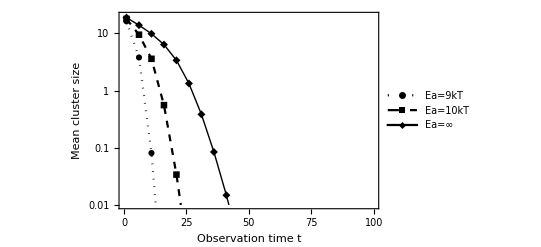

```mathematica
ListLogPlot[
{
Table[{tx, mAveF[tx, 10, 10,  9, 20]}, {tx, 1, 100, 5}],
Table[{tx, mAveF[tx, 10,  10, 10, 20]}, {tx, 1, 100, 5}],
Table[{tx, mAveFInfEa[tx, 10,  10, 20]}, {tx, 1, 100, 5}]
}, 
PlotRange->{{0, 100},{0.01, 20}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Mean cluster size"}
]
```

```mathematica
pdf[50, 20,  7,  10.0]
```

3.906×10^-9

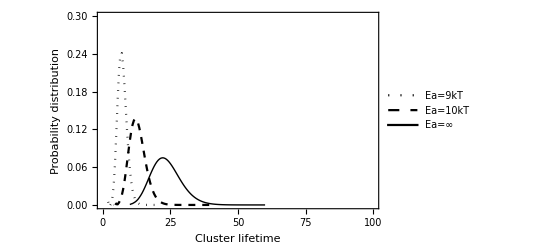

```mathematica
ListPlot[
{
Table[{tx, pdf[tx, 20,  10,  10, 9]}, {tx, 2, 20, 0.5}],
Table[{tx, pdf[tx, 20,   10, 10, 10]}, {tx, 4, 40, 0.5}],
Table[{tx, pdf[tx, 20,   10, 10, 200]}, {tx, 10, 60, 0.5}]
}, 
(*PlotRange->{0.01, 20},*)
PlotRange->{{0, 100},{0, 0.3}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
(*PlotMarkers->Automatic,*)
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Cluster lifetime", "Probability distribution"}
]
```

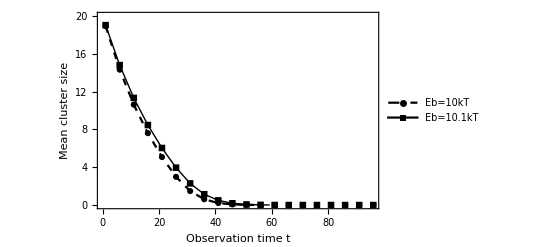

```mathematica
ListPlot[
{
Table[{tx, mAveFInfEa[tx, 10, 7,   20]}, {tx, 1, 100, 5}],
Table[{tx, mAveFInfEa[tx, 10.1,  7,  20]}, {tx, 1, 100, 5}]
(*Table[{tx, mAveFInfEa[tx, 10,  7, 20]}, {tx, 1, 100, 5}]*)
}, 
PlotRange->{0.01, 20},
PlotLegends->Placed[{"Eb=10kT", "Eb=10.1kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Mean cluster size"}
]
```

General::munfl: Exp[-739.696] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1997.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

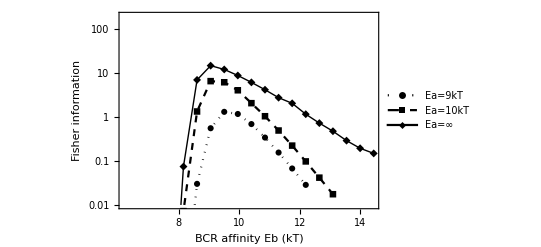

```mathematica
ListLogPlot[
{
Table[{ebx, fisherInfoF[10, ebx,  9, 7, 20]}, {ebx, 5, 12.5, 0.45}],
Table[{ebx, fisherInfoF[10, ebx,  10, 7, 20]}, {ebx, 5, 13.5, 0.45}],
Table[{ebx, fisherInfoFInfEa[10, ebx,  7, 20]}, {ebx, 5, 14.5, 0.45}]
}, 
PlotRange->{0.01, 200},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"BCR affinity Eb (kT)", "Fisher information"}
]
```

```mathematica
infoPerCluster0F = Table[{ncx,fisherInfoF[10, 10, 200, 0, ncx]/ncx}, {ncx, 2, 29}]
```

{{2,0.358713},{3,0.358713},{4,0.358713},{5,0.358713},{6,0.358713},{7,0.358713},{8,0.358713},{9,0.358713},{10,0.358713},{11,0.358713},{12,0.358713},{13,0.358713},{14,0.358713},{15,0.358713},{16,0.358713},{17,0.358713},{18,0.358713},{19,0.358713},{20,0.358713},{21,0.358713},{22,0.358712},{23,0.358713},{24,0.358717},{25,0.358703},{26,0.358721},{27,0.358747},{28,0.358685},{29,0.358769}}

```mathematica
infoPerClusterE12FInfEa = Table[{ncx, fisherInfoFInfEa[10, 12, 10, ncx]/ncx}, {ncx, 2, 16}]
```

{{2,0.418996},{3,0.326994},{4,0.220329},{5,0.165228},{6,0.137146},{7,0.120856},{8,0.110238},{9,0.102752},{10,0.0971797},{11,0.0929298},{12,0.0893732},{13,0.0863827},{14,0.0909032},{15,0.0784047},{16,0.0759241}}

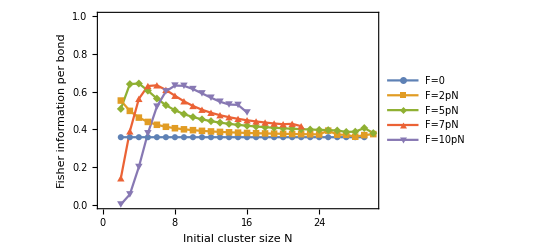

```mathematica
ListPlot[{
infoPerCluster0F,
infoPerCluster2FInfEa,
infoPerCluster5FInfEa,
infoPerCluster7FInfEa,
infoPerCluster10FInfEa
}, Joined->True, PlotMarkers->Automatic, PlotRange->{0, 1},

PlotLegends->Placed[{"F=0", "F=2pN", "F=5pN", "F=7pN", "F=10pN"},{0.8, 0.7}],
(*PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},*)
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Initial cluster size N", "Fisher information per bond"}
]
```

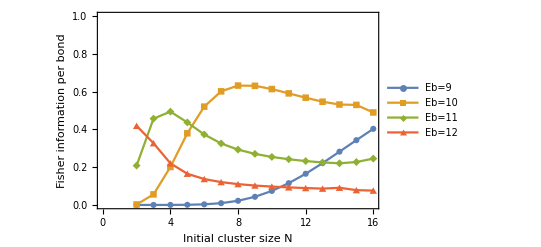

```mathematica
ListPlot[{
(*infoPerCluster0F,*)
(*infoPerClusterE8FInfEa,*)
infoPerClusterE9FInfEa,
infoPerCluster10FInfEa,
infoPerClusterE11FInfEa,
infoPerClusterE12FInfEa
}, Joined->True, PlotMarkers->Automatic, PlotRange->{0, 1},

PlotLegends->Placed[{"Eb=9", "Eb=10", "Eb=11", "Eb=12"},{0.8, 0.7}],
(*PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},*)
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Initial cluster size N", "Fisher information per bond"}
]
```

```mathematica
fisherInfoFInfEa[20, 10, 5, 10]
```

7.23065

```mathematica
fisherInfoF[20, 10, 10, 0, 10]
```

1.60177

General::munfl: Exp[-834.916] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.587] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-834.916] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

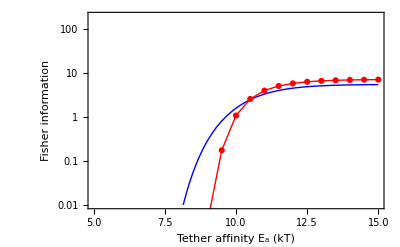

```mathematica
Show[
LogPlot[
{
fisherInfo2[20, 10, ebx, 10]
(*fisherInfo2[50, 10, ebx, 20],
fisherInfo2[50, 10, ebx, 20]*)
}, {ebx, 5, 15},
PlotRange->{0.01, 200},
PlotStyle->{{Blue, Thick}}
],
ListLogPlot[
Table[{eax,fisherInfoF[20, 10, eax, 5, 10]}, {eax, 5, 15, 0.5}],
Joined->True, PlotMarkers->Automatic, PlotStyle->{Red, Thick}
],
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Tether affinity E_a (kT)", "Fisher information"}

]
```

## Calculate lower bound

```mathematica
Integrate[n b t e^{-b t} (1-e^{-b t})^(n-1), {t, 0, Infinity}]
```

{∫_0^∞ b e^(-b t) (1-e^(-b t))^(-1+n) n tⅆt}

```mathematica
lifetime[Ea_, Eb_]
```

```mathematica
Plot[]
```

```mathematica
Solve[n b t e^{-b t} (1-Exp[-b t])^(n-1)==0, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0},{t→Log[1/(1-0^(1/(-1+n)))]/b}}

```mathematica
D[n b  Exp[-b t] (1-Exp[-b t])^(n-1), t]
```

-b^2 ⅇ^(-b t) (1-ⅇ^(-b t))^(-1+n) n+b^2 ⅇ^(-2 b t) (1-ⅇ^(-b t))^(-2+n) (-1+n) n

```mathematica
Solve[-b^2 ⅇ^(-b t) (1-ⅇ^(-b t))^(-1+n) n+b^2 ⅇ^(-2 b t) (1-ⅇ^(-b t))^(-2+n) (-1+n) n==0, t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1])/b, C[1]∈ℤ&&Re[n]>2]},{t→ConditionalExpression[(2 ⅈ π C[1]+Log[n])/b, C[1]∈ℤ]}}

```mathematica
Simplify[]
```